```mathematica
ϵ=.01
```

0.01

```mathematica
NDSolve[{u''[t]+(1+ϵ Sin[ϵ t])u[t]+ϵ(u'[t])^3==0,u[0]==1,u'[0]==0},u[t],{t,0,500}]
```

{{u[t]→InterpolatingFunction[{{0., 500.}}, <>][t]}}

```mathematica
%19⟦1,1,2⟧
```

InterpolatingFunction[{{0., 500.}}, <>][t]

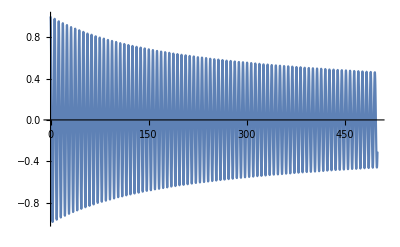

```mathematica
Plot[%20,{t,0.,500.}]
```

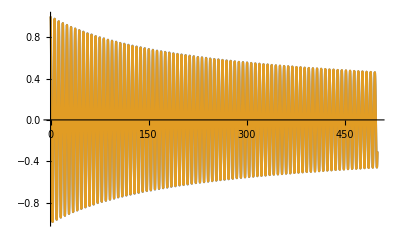

```mathematica
Plot[{2/Sqrt[4+3ϵ t] Cos[t+1/2-Cos[ϵ t]/2],%20},{t,0,500}]
```

```mathematica
Show[%22,ImageSize->Full]
```

-Graphics-

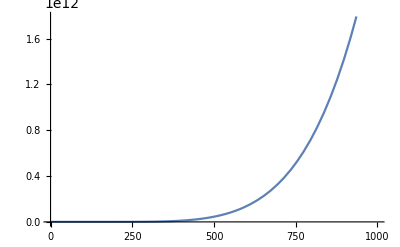

```mathematica
Plot[%5,{t,0.,1000.}]
```

```mathematica
a=-1
```

-1

Out::intm: Machine-sized integer expected at position 1 in Out[51.].

General::stop: Further output of Out::intm will be suppressed during this calculation.

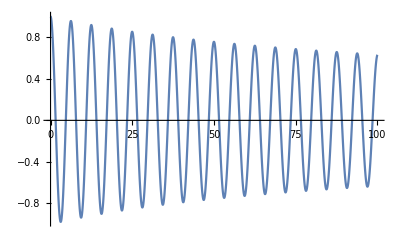

```mathematica
Plot[{2/Sqrt[4-3 a(a^2+1)ϵ t] Cos[t+1/(2 a)Log[Abs[4/(3 a ϵ t(a^2+1)-4)]]],%51},{t,0,100}]
```

```mathematica
Show[%38,ImageSize->Full]
```

-Graphics-

```mathematica
NDSolve[{u''[t]+u[t]+ϵ (u[t]-a u'[t])^3==0,u[0]==1,u'[0]==0},u[t],{t,0,100}]
```

NDSolve::ndsz: At t == 67.5978, step size is effectively zero; singularity or stiff system suspected.

{{u[t]→InterpolatingFunction[{{0., 67.5978}}, <>][t]}}

```mathematica
%50⟦1,1,2⟧
```

InterpolatingFunction[{{0., 67.5978}}, <>][t]

```mathematica
Plot[%51,{t,0.,100.}]
```

-Graphics-

```mathematica
NDSolve[v[r,s]==4D[D[v[r,s],r],s],v[r,s],{r,-100,100},{s,-100,100}]
```

NDSolve::femibcnd: No DirichletCondition or Robin-type NeumannValue was specified for {v}; the result is not unique up to a constant.

{{v[r,s]→InterpolatingFunction[{{-100., 100.}, {-100., 100.}}, <>][r,s]}}

```mathematica
%56⟦1,1,2⟧
```

InterpolatingFunction[{{-100., 100.}, {-100., 100.}}, <>][r,s]

```mathematica
NDSolve[{u''[t]+u[t]+.01(u[t])^3==Cos[t],u[0]==1,u'[0]==0},u[t],{t,0,100}]
```

{{u[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}}

```mathematica
%1⟦1,1,2⟧
```

InterpolatingFunction[{{0., 100.}}, <>][t]

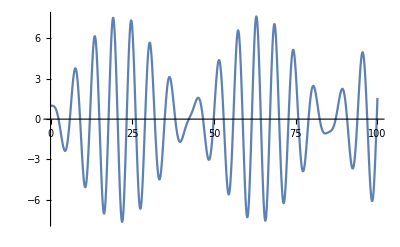

```mathematica
Plot[%2,{t,0.,100.}]
```

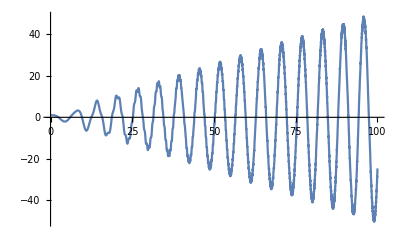

```mathematica
Plot[t/2 Sin[t]+Cos[t+((3t^2)/8+3/4)(.01)t],{t,0,100}]
```

```mathematica
NDSolve[{u''[t]+u[t]+.01(u[t])^3==Cos[4t],u[0]==1,u'[0]==0},u[t],{t,0,100}]
```

{{u[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}}

```mathematica
%9⟦1,1,2⟧
```

InterpolatingFunction[{{0., 100.}}, <>][t]

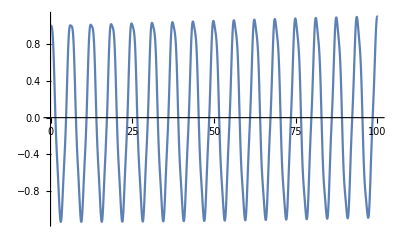

```mathematica
Plot[%10,{t,0.,100.}]
```

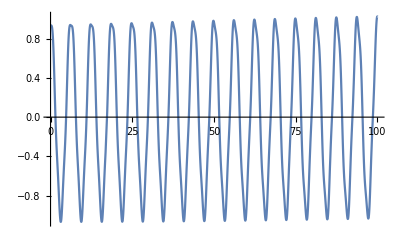

```mathematica
Plot[(-Cos[4 t])/(4^2-1)+Cos[t+(3/(4(4^2-1)^2)+3/8)(.01)t],{t,0,100}]
```

```mathematica
NDSolve[{u''[t]+u[t]+.01(u[t])^3==1,u[0]==1,u'[0]==0},u[t],{t,0,100}]
```

{{u[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}}

```mathematica
%13⟦1,1,2⟧
```

InterpolatingFunction[{{0., 100.}}, <>][t]

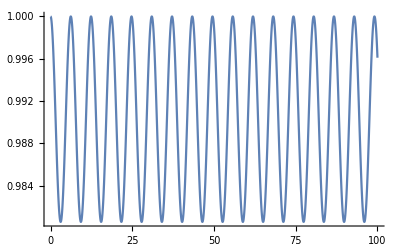

```mathematica
Plot[%14,{t,0.,100.}]
```

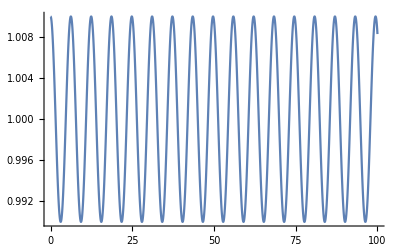

```mathematica
Plot[1+(.01)Cos[t+(3/4+3/8)(.01)t],{t,0,100}]
```